# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Poincare\alfa 0.84 and k 20\Frames

```mathematica
LaunchKernels[16]
```

{Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16)}

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];


Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=GoldenRatio;
τ=1;
```

```mathematica
(*randomregion=RandomPoint[Disk[{0,0},1.999],350];*)
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
randomregion=Table[{i,0},{i,0,1.999,0.02}];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=(rot[θ+Pi/4].#&/@randomregion);
randomregion=Join[randomregion,randomregionb];
randomregiondos=Table[{0,i},{i,0,1.999,0.02}];
randomregion=Join[randomregion,randomregiondos];
randomregionc=-randomregion;
randomregion//Length
```

300

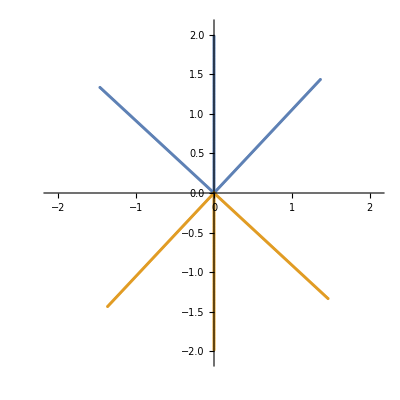

```mathematica
ListPlot[{randomregion,randomregionc},AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
```

```mathematica
GoldenRatio//N
```

1.61803

```mathematica
α=GoldenRatio;
klist=Table[i,{i,α/20,40α,α/20}];
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregionc}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregionc]*(kicks+1),2}];
poincareb=Graphics[{PointSize[0.0010],Red,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[klist[[j]]]]<>"_kicks_"<>ToString[kicks]<>"_frame"<>ToString[j]<>".png",Show[{poincarea,poincareb}]];
,{j,Length[klist]}]
```

$Aborted

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],1000];
```

```mathematica
puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,20.,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[20.],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[20.]]<>"_kicks_"<>ToString[kicks]<>"_frameb"<>ToString[248]<>".png",poincarea];
```